Reinforcement reinforcement learning
070421 
v1
Faiz Ikramulla

```mathematica
(*setting the backgorund color of the notebook for contrast*)
SetOptions[SelectedNotebook[],Background->LightOrange];
```

DeviceObject[…]

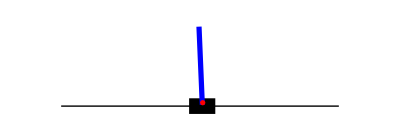

```mathematica
(*setting up the environment - cartpole here*)
env=DeviceOpen["SimulatedCartPole"]
DeviceExecute[env,"Render"]
```

```mathematica
(*setting up the policy definition - which is a chain of nets*)

policyNet=NetInitialize@NetChain[{64,Tanh,2,SoftmaxLayer[]},"Input"->4,"Output"->NetDecoder[{"Class",{Left,Right}}]]
```

NetChain[<>]

Loss Function Definition

```mathematica
(*loss function defined here*)

reinforceLoss=NetGraph[{CrossEntropyLossLayer["Index"],ThreadingLayer[#1*#2&]},{NetPort["DiscountedReward"]->2,{NetPort["Input"],NetPort["Action"]}->1->2},"Action"->NetEncoder[{"Class",{Left,Right}}]]
```

NetGraph[<>]

```mathematica
(*this is just a comment*)
```

NetGraph::noinfo: Input expression NetGraph[<>] contains insufficient information to interpret the result.

```mathematica
(*this is just a comment*)
```